This script is a part of ANGEL project.
V 1.0
2017.10.01
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Variables clearing *)
```

```mathematica
importFile="Data.dat";(* Getting datafile name *)
```

```mathematica
Data=Import[FileNameJoin[{NotebookDirectory[],importFile}]];(* Importing data from a file *)
NewData=Data;(* Preparing new data *)
```

```mathematica
addToRow=2;(* Adding values to certain row *)
startFromLie=2;(* Lines before this are overhead *)
addFromLine=6413;(* Adding values from certain line *)
adding=0.1;(* Adding value *)
```

```mathematica
For[i=startFromLie,i≤Length[NewData],i+=1,If[i≥ addFromLine,NewData[[i,addToRow]]+=adding,False]];(* Adding *)
```

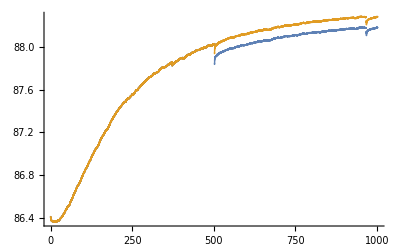

```mathematica
ListPlot[Evaluate[{
Transpose[{Data[[startFromLie;;]][[All,1]],Data[[startFromLie;;]][[All,addToRow]]}],Transpose[{NewData[[startFromLie;;]][[All,1]],NewData[[startFromLie;;]][[All,addToRow]]}]
}],PlotRange->All](* Plotting old and new data for comparison *)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"New_"<>importFile}],NewData];(* Export corrected data *)
```